```mathematica
Pf1=Import["Pf1.txt","Table"];
Pf2=Import["Pf2.txt","Table"];
Pe=Import["Pe.txt","List"];
```

```mathematica
mmp={};
For[nn=0,nn≤45,nn++,
{
Clear[V];
μ=50;
(*nn=1;*)
(*wc=μ/(nn+1);*)
wc=μ/(nn+5/4);
{me,ϵ,V,q}={1,0.1,1,1};
data={};
(*For[V=0.01,V≤π,V+=0.05,*)
For[ϵ=0.0,ϵ≤1,ϵ+=0.1,
{
l=1/Sqrt[me*wc];
En[n_]:=(n+1/2)*wc;
kf[n_]:=Re[Sqrt[2*(μ-En[n])]];
selfenergy[n_]:=-0.5*V*q^2*l^2*(1/2π)*Sum[1/(2^(n+m)*(n!)*(m!))*Pf1[[n+1,m+1]],{m,0,nn+1}];
smatrix=Table[(selfenergy[n]-selfenergy[n+1])*KroneckerDelta[n,m],{n,0,nn},{m,0,nn}];
vmatrix=Table[(1/l)*Pf2[[n+1,m+1]],{n,0,nn},{m,0,nn}];
kmatrix=Table[(1/π)*(kf[n]-kf[n+1])*KroneckerDelta[n,m],{n,0,nn},{m,0,nn}];
M=V*(kmatrix.vmatrix+smatrix);
ΔE[n_]:=(l^4)*(ϵ/4)*Pe[[n+1]];
MX[i_,j_]:=Minors[M][[nn+2-i,nn+2-j]];
δω=-(Sum[(ΔE[i+1]-ΔE[i])*MX[i+1,i+1]/(kf[i+1]-kf[i]),{i,0,nn}])/(Sum[MX[i+1,i+1]/(kf[i+1]-kf[i]),{i,0,nn}]);
(*AppendTo[data,{V*me/π,δω/wc}];*)
AppendTo[data,{ϵ,δω/wc}];
}];
line=Fit[data,{x},x];
AppendTo[mmp,{nn+1,line/x}];}]
```

```mathematica
line=Fit[data,{x},x]
```

-0.0000495553 x

```mathematica
line/x
```

-0.0000495553

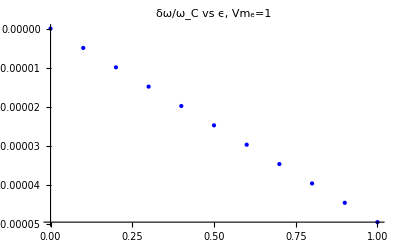

```mathematica
g1=ListPlot[data,PlotStyle->Blue,PlotRange->Automatic,PlotLabel->"δω/ω_C vs ϵ, Vm_e=1"]
```

```mathematica
EmitSound[Play[Sin[1200t+1000*Sqrt[t]+500*t^2],{t,0,3}]]
```